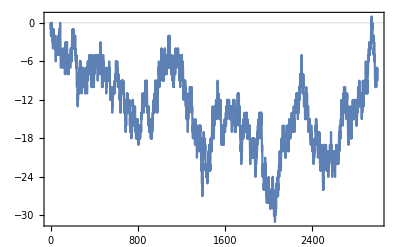

```mathematica
race=ListLinePlot[Accumulate[Mod[Prime[Range[2,3000]],4,-1]],Frame->True,Axes
->False,GridLines->{{},{0}}]
```

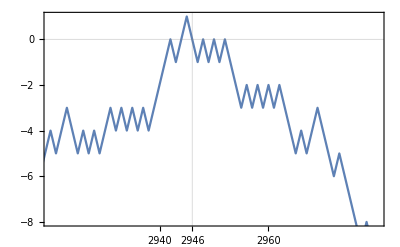

```mathematica
Show[race,PlotRange->{{2920,2980},{-8,1}},GridLines->{{2946},{0}},FrameTicks->{{Automatic,None},{{2940,2946,2960},{None}}}]
```

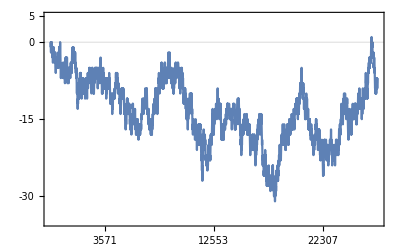

```mathematica
ListLinePlot[Accumulate[Mod[Prime[Range[2,3000]],4,-1]],Frame->True,Axes
->False,GridLines->{{},{0}},FrameTicks->{{{-30,-15,0,5},{}},{Append[Table[{n-1,Prime[n]},{n,500,2500,500}],{2945,Prime[2946]}],{}}},PlotRange->{-35,5}]
```